```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ExpandFileName["D:\\KloostBH\\Final"]
```

D:\KloostBH\Final

## Common functions

### Modular

```mathematica
Δ1[q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^24
Δ2[q_]:=DedekindEta[1/(π ⅈ)Log[q]]^24
polar[w_] := CoefficientList[q^(-(2 w)/24) DeleteCases[Assuming[q>0,Series[Δ1[q]^((2 w)/24),{q,0,0}]]//Normal, _Integer], q]
```

### Mock modular

```mathematica
E2[q_] := 1-24Sum[(n q^n)/(1-q^n) ,{n,1,500}]
```

```mathematica
kfnc[w_,x_,y_,c_]:=ⅈ^-w Total[ Flatten[ Table[ If[GCD[c,d]==1 && Mod[(a*d-1),c]==0,Exp[2π ⅈ(a/c y+d/c x)],0] ,{d,-c,-1},{a,0,c-1} ] ] ]
```

mp1 is the analog I_11 in C.8 of 2112.10023. mp2 is the analog of I_12.

```mathematica
m0[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], {c,1,10}]
```

```mathematica
m0l[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], n->0 ], {c,1,10}]
```

```mathematica
mp1[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp2[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp1l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp2l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp1re[n_,n1_ , w_] :=Re[mp1[n,n1,w]]
mp1abs[n_,n1_ , w_] :=Abs[mp1[n,n1,w]]
mp2re[n_,n1_ , w_] :=Re[mp2[n,n1,w]]
mp2abs[n_,n1_ , w_] :=Abs[mp2[n,n1,w]]
```

```mathematica
mp1lre[n_,n1_ , w_] :=Re[mp1l[n,n1,w]]
mp1labs[n_,n1_ , w_] :=Abs[mp1l[n,n1,w]]
mp2lre[n_,n1_ , w_] :=Re[mp2l[n,n1,w]]
mp2labs[n_,n1_ , w_] :=Abs[mp2l[n,n1,w]]
```

```mathematica
cn0[n_, n1_, w_] := If[n==0,  m0l[n,n1,w],m0[n,n1,w]]  (* Or you can directly put 0 for n=0*)
```

```mathematica
cn1[n_, n1_, w_] := If[n==0,  mp1l[n,n1,w],mp1[n,n1,w]]
cn1re[n_, n1_, w_] := If[n==0,  mp1lre[n,n1,w],mp1re[n,n1,w]]
cn1abs[n_, n1_, w_] := If[n==0,  mp1labs[n,n1,w],mp1abs[n,n1,w]]
```

```mathematica
cn2[n_, n1_, w_] := If[n==0,  mp2l[n,n1,w],mp2[n,n1,w]]
cn2re[n_, n1_, w_] := If[n==0,  mp2lre[n,n1,w],mp2re[n,n1,w]]
cn2abs[n_, n1_, w_] := If[n==0,  mp2labs[n,n1,w],mp2abs[n,n1,w]]
```

```mathematica
ψ0[n_, w_] := Total[Table[ polar[w][[i]] cn0[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ1[n_, w_] := Total[Table[ polar[w][[i]] cn1[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1re[n_, w_] := Total[Table[ polar[w][[i]] cn1re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1abs[n_, w_] := Total[Table[ polar[w][[i]] cn1abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ2[n_, w_] := Total[Table[ polar[w][[i]] cn2[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2re[n_, w_] := Total[Table[ polar[w][[i]] cn2re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2abs[n_, w_] := Total[Table[ polar[w][[i]] cn2abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

### Jacobi

```mathematica
datadefn[rawData_,minLen_]:=Module[{newkeysTemp,newKeys,newVals,data},
newkeysTemp = If[Length[#]>= minLen, #, ##&[] ] & /@ Keys[rawData];
newKeys =newkeysTemp[[All,;;minLen]];
newVals = If[Length[Keys[#]]>= minLen, Values[#], ##&[] ] & /@ rawData;
data = Thread[newKeys ->newVals];
Return[data]
]
```

```mathematica
allprodθ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt = Thread[cq -> wt];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1[k_,nq_,nu_]:=allprodθ[1,k,2, 0, 3, 0, 4, 0, nq, nu]
theta2[l_,nq_,nu_]:=allprodθ[1,0,2, l, 3, 0, 4, 0, nq, nu]
theta3[m_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, m, 4, 0, nq, nu]
theta4[n_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, 0, 4, n, nq, nu]
```

```mathematica
allprodθbyΔ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}]];
th2  = If[k<0, u^-k th1 ,th1 ];
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1byΔ[k_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,k,2, 0, 3, 0, 4, 0, nq, nu,qInPower]
theta2byΔ[l_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, l, 3, 0, 4, 0, nq, nu,qInPower]
theta3byΔ[m_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, m, 4, 0, nq, nu,qInPower]
theta4byΔ[n_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, 0, 4, n, nq, nu,qInPower]
```

```mathematica
klmn[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
```

```mathematica
powers[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]>0]
```

```mathematica
allprodgen[nq_,nu_,pwrlist_]:=Module[{tempser,i,filename,str},
filename=NotebookDirectory[]<>"jacobi-klmn.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
Do[
tempser=allprodθ@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];Write[str,{i, pwrlist[[i]],Keys[tempser], Values[tempser]}]
,{i,Length[pwrlist]}
];
Close[filename];
]
```

### ML

```mathematica
leakyRelu[α_]:=ElementwiseLayer[If[#>0,#,α #]&]
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
datapartition[data_]:=With[{datasize=Length[data]},
Module[{trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]],valpos,testpos,traindata,valdata,testdata},
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
traindata=data[[trainpos]];valdata=data[[valpos]];testdata=data[[testpos]];
Return[{traindata,valdata,testdata}]
]
]
```

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

## Modular forms from powers of Δ

## Half-integer negative powers, first few coefficients

```mathematica
minweight=-200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, -1/2, minweight, -1/2}];
```

```mathematica
dnexactw200norm20=Normalize/@dnexactw200[[;;,;;20]];
```

```mathematica
(*Rule@@{a,b}*)
```

```mathematica
(*Apply[Rule,dnexactw200[[;;10]],1]*)
```

```mathematica
weights=Table[w,{w,-1/2, minweight, -1/2}];
```

```mathematica
data=Thread[dnexactw200[[;;,;;20]]->weights];
```

```mathematica
data=datapartition[data];
```

```mathematica
datanorm=datapartition[Thread[dnexactw200norm[[;;,;;20]]->weights]];
```

```mathematica
datanorm20=datapartition[Thread[dnexactw200norm20->weights]];
```

```mathematica
Length/@data
Length/@datanorm
```

{282,57,38}

{282,57,38}

```mathematica
{traindata,valdata,testdata}=data;
{traindatanorm,valdatanorm,testdatanorm}=datanorm;
```

```mathematica
{traindatanorm20,valdatanorm20,testdatanorm20}=datanorm20;
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->Length[Keys@traindata[[1]]], "Output"->"Scalar"];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=12500;
```

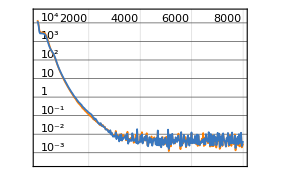
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:40000  rounds:8000  time:53s  examples/s:48465
data | ,,  training examples:282  validation examples:57  processed examples:2560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.06×10^-3
validation | ,,  loss:1.21×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm20,All,ValidationSet->valdatanorm20,MaxTrainingRounds->epoch,LearningRate->.0001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{-33/2,-22,-29,-30,-63/2,-79/2,-41,-87/2,-127/2,-68,-151/2,-153/2,-86,-87,-177/2,-91,-93,-98,-203/2,-104,-110,-127,-275/2,-283/2,-287/2,-149,-154,-156,-327/2,-164,-333/2,-167,-172,-363/2,-184,-373/2,-192,-391/2}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{-16.4678,-22.002,-28.9855,-30.0236,-31.4576,-39.4436,-40.9391,-43.5369,-63.4645,-68.0172,-75.5254,-76.5019,-85.944,-86.8839,-88.4146,-91.0245,-93.0518,-98.0103,-101.532,-104.027,-109.946,-126.974,-137.512,-141.497,-143.503,-148.947,-154.026,-156.014,-163.503,-163.999,-166.448,-166.934,-172.011,-181.47,-183.969,-186.508,-192.025,-195.514}

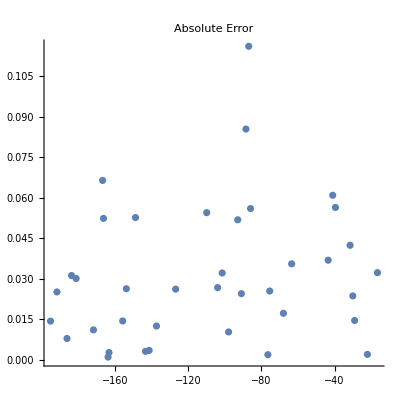

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

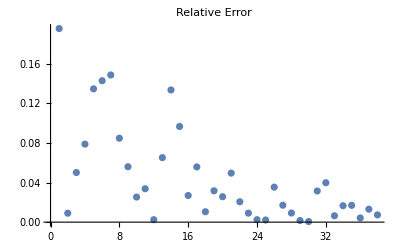

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0444724

## Real negative powers (chosen at random)

```mathematica
minweight = -300;
coeffnum=50;
datasize=500;
```

```mathematica
weights=Rationalize[SetPrecision[RandomReal[{minweight,-0.01},datasize], 4], 0];
```

```mathematica
dnexactwrandom = ParallelTable[ If[Mod[weights[[i]],12]==0,  CoefficientList[Assuming[q>0,q^(-(2weights[[i]])/24) Series[(Δ1[q])^((2 weights[[i]])/24),{q,0,coeffnum-Length[polar[weights[[i]]]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2weights[[i]])/24) Series[(Δ1[q])^((2 weights[[i]])/24),{q,0,coeffnum-Length[polar[weights[[i]]]]}]//Normal], q]],{i,datasize}];
```

```mathematica
dnexactwrandomnorm20=Normalize/@dnexactwrandom[[;;,;;20]];
```

```mathematica
datanorm20=datapartition[Thread[dnexactwrandomnorm20->weights]];
```

```mathematica
Length/@datanorm20
```

{375,75,50}

```mathematica
{traindatanorm20,valdatanorm20,testdatanorm20}=datanorm20;
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=8500;
```

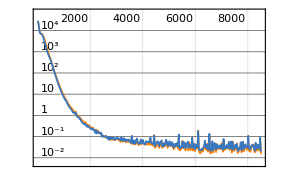
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:51000  rounds:8500  time:1.2min  examples/s:45766
data | ,,  training examples:375  validation examples:75  processed examples:3264000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.42×10^-2
validation | ,,  loss:1.89×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm20,All,ValidationSet->valdatanorm20,MaxTrainingRounds->epoch,LearningRate->.0001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{-3046/11,-1745/8,-3042/11,-497/6,-299/8,-811/3,-866/7,-799/6,-4357/21,-1139/19,-233/16,-179/3,-678/7,-1011/4,-763/15,-985/6,-853/4,-279/2,-1715/9,-736/7,-793/4,-1417/7,-151/27,-1239/5,-1081/5,-1530/23,-859/6,-1109/4,-1787/20,-4229/15,-1311/5,-2553/20,-134/27,-1588/17,-1825/8,-243/4,-1491/16,-752/7,-1115/4,-666/7,-2651/13,-4178/15,-739/5,-301/4,-544/13,-1137/4,-203/19,-509/4,-667/9,-1039/4}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{-276.897,-218.034,-276.529,-82.5552,-37.3054,-270.334,-123.862,-132.946,-207.451,-59.9074,-14.5591,-59.631,-97.0301,-252.721,-51.0785,-164.011,-213.292,-139.292,-190.535,-105.146,-198.35,-202.403,-5.37989,-247.756,-216.182,-66.3861,-143.219,-277.241,-89.2658,-282.022,-262.139,-127.743,-4.86398,-93.5382,-228.142,-60.6949,-93.3068,-107.296,-278.746,-95.3076,-203.822,-278.529,-147.997,-75.3299,-42.0091,-284.406,-10.748,-127.356,-74.2008,-259.74}

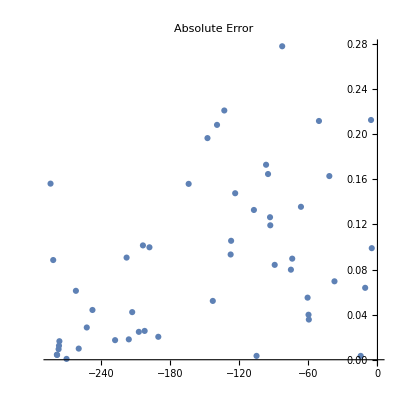

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

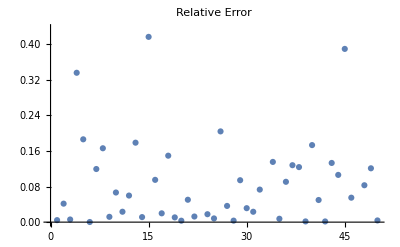

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.20917

## Half-integer positive powers

```mathematica
maxweight=200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, 1/2, maxweight,1/2}];
```

```mathematica
dnexactw200norm20=Normalize/@dnexactw200[[;;,;;20]];
```

```mathematica
weights=Table[w,{w,1/2, maxweight,1/2}];
```

```mathematica
datanorm20=datapartition[Thread[dnexactw200norm20->weights]];
```

```mathematica
{traindatanorm20,valdatanorm20,testdatanorm20}=datanorm20;
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
enc20=enc[datanorm20]
```

NetEncoder[…]

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->enc[datanorm20],"Output"->"Scalar"];
```

```mathematica
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=8500;
```

```mathematica
result=NetTrain[KlNet,traindatanorm20,All,ValidationSet->valdatanorm20,MaxTrainingRounds->epoch,LearningRate->.0001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

NetTrain::encgenfail1: Could not encode training input number 142 for port "Input": "Function" encoder did not produce an output that was a length-300 vector of real numbers. Please check the example.

$Failed

Set::shape: Lists {wNet,valLosses} and $Failed[{TrainedNet,ValidationLossList}] are not the same shape.

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{1/2,7/2,6,8,14,37/2,21,45/2,30,39,42,85/2,87/2,44,97/2,105/2,57,61,129/2,67,137/2,143/2,147/2,79,181/2,98,107,115,125,127,255/2,277/2,141,147,349/2,357/2,179,187,379/2,199}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{46.903,3.92553,6.20562,8.7472,11.4754,20.119,20.5398,22.3093,29.8257,38.8687,42.01,42.9627,44.2719,43.9857,49.1039,52.3629,56.848,60.9243,63.4096,67.8703,68.1667,71.4386,73.4138,78.9211,90.4117,98.0252,107.051,114.926,125.019,127.04,127.535,138.519,141.068,147.063,174.602,178.564,179.075,187.085,189.592,199.015}

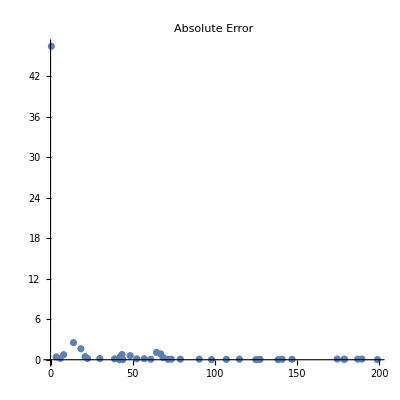

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

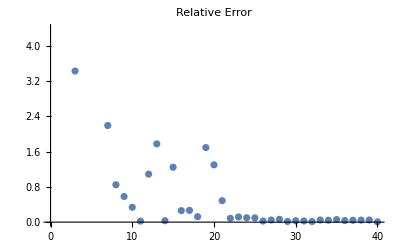

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

233.638

## Randomly chosen slice of coefficients

```mathematica
minweight=-200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, -1/2, minweight, -1/2}];
```

```mathematica
numsamp=20;
```

```mathematica
weights=Table[w,{w, -1/2, minweight, -1/2}];
```

```mathematica
randsamp=Sort[RandomSample[Range[coeffnum],numsamp]]
```

{3,4,7,8,11,12,13,18,19,20,22,23,25,27,30,31,32,34,37,39}

```mathematica
datarandom=Normalize/@dnexactw200[[;;,randsamp]];
```

```mathematica
data=datapartition[Thread[datarandom->weights]];
```

```mathematica
{traindata,valdata,testdata}=data;
{traindatanorm,valdatanorm,testdatanorm}=datanorm;
```

```mathematica
{traindatanorm20,valdatanorm20,testdatanorm20}=datanorm20;
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->Length[Keys@traindata[[1]]], "Output"->"Scalar"];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=12500;
```

```mathematica
result=NetTrain[KlNet,traindatanorm20,All,ValidationSet->valdatanorm20,MaxTrainingRounds->epoch,LearningRate->.0001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

## Mock modular forms

## Generating data for negative weights

```mathematica
minweight = -100;
coeffnum=50;
```

```mathematica
cne50w100 = ParallelTable[ If[Mod[w,12]==0,  coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal,q], coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal,q]],{w, -1/2,minweight, -1/2}];
```

```mathematica
w100 = Table[w, {w, -1/2, minweight, -1/2}];
```

## Normalized 10 coefficients

```mathematica
cne50w100norm10=Normalize/@cne50w100[[;;,;;10]];
```

```mathematica
data=MapThread[Rule,{cne10w100,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->10,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

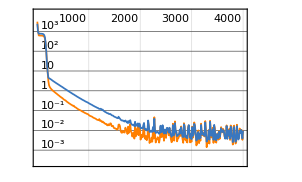
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:15s  examples/s:53452
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.87×10^-2
validation | ,,  loss:2.75×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-19,-55/2,-30,-31,-45,-49,-103/2,-111/2,-57,-71,-79,-165/2,-83,-86,-181/2,-189/2,-96}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-11.8579,-18.9686,-27.5082,-30.0013,-31.0176,-45.0016,-49.0026,-51.5023,-55.5074,-57.0019,-71.0107,-79.0108,-82.5823,-83.0482,-85.963,-90.5124,-94.4849,-95.9833}

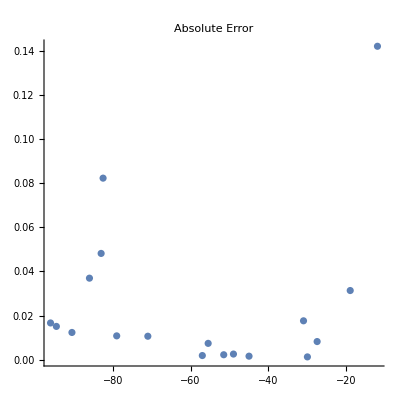

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

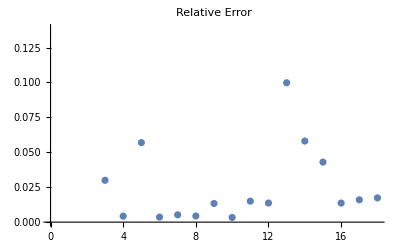

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0970438

## Normalized 30 coefficients

```mathematica
cne50w100norm30=Normalize/@cne50w100[[;;,;;30]];
```

```mathematica
data=MapThread[Rule,{cne50w100norm30,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

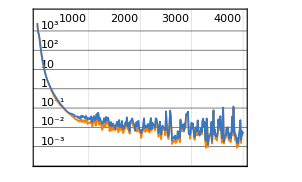
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:46363
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.13×10^-4
validation | ,,  loss:5.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-4,-9/2,-10,-11,-19,-45/2,-35,-36,-41,-87/2,-49,-103/2,-62,-64,-66,-159/2,-173/2,-89,-181/2,-91}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-4.01904,-4.50736,-9.99175,-10.9861,-18.9724,-22.478,-34.9868,-35.9882,-40.9995,-43.4913,-48.993,-51.4901,-61.9679,-64.0045,-65.9944,-79.508,-86.5306,-89.0009,-90.4528,-90.9761}

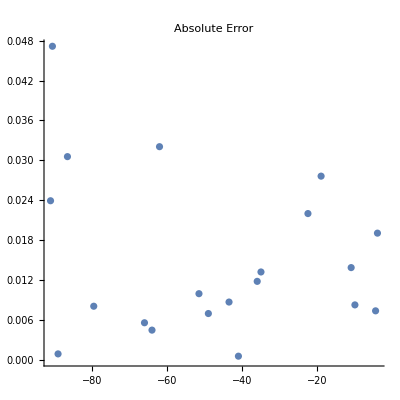

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

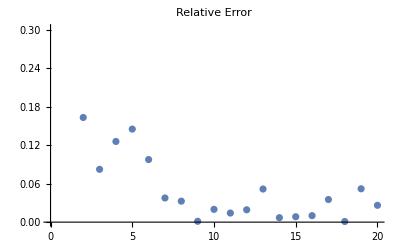

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0704135

## 30 coefficients starting at 11th coefficient

```mathematica
cne50w100norm11to40=Normalize/@cne50w100[[;;,11;;40]];
```

```mathematica
data=MapThread[Rule,{cne50w100norm11to40,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

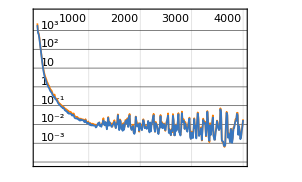
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:45839
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.86×10^-3
validation | ,,  loss:2.36×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-1,-17/2,-19/2,-13,-29/2,-39/2,-45/2,-25,-51/2,-65/2,-33,-71/2,-43,-44,-61,-123/2,-71,-187/2,-94,-199/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-0.984623,-8.48011,-9.48186,-12.9901,-14.5167,-19.476,-22.4832,-24.9928,-25.4965,-32.5007,-32.9923,-35.4475,-43.0156,-44.003,-61.0033,-61.5056,-70.9836,-93.4771,-93.9854,-99.4147}

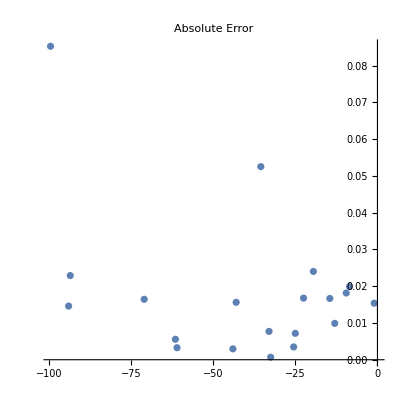

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

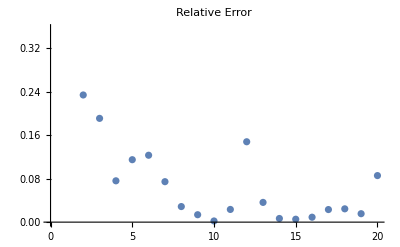

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.138669

## Generating data for positive weights

```mathematica
maxweight = 100;
coeffnum=50;
```

```mathematica
cne50w100plus = ParallelTable[ If[Mod[w,12]==0,  coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal,q], coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal,q]],{w, 0,maxweight,1/2}];
```

```mathematica
w100plus = Table[w, {w, 0,maxweight,1/2}];
```

## Normalized 30 coefficients

```mathematica
cne50w100plusnorm30=Normalize/@cne50w100plus[[;;,;;30]];
```

```mathematica
data=MapThread[Rule,{cne50w100plusnorm30,w100plus}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

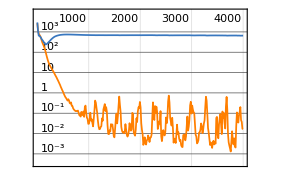
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:45601
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:8.04×10^-3
validation | ,,  loss:6.59×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

## Coefficients calculated via Kloosterman sums

```mathematica
minweight = -100;
coeffnum=30;
```

```mathematica
cn0c30w100 = Table[If[Mod[w,12]==0,Table[ ψ0[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ0[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
cn0c30w100norm30=Normalize/@cn0c30w100;
```

```mathematica
data=MapThread[Rule,{cn0c30w100norm30,wlist}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

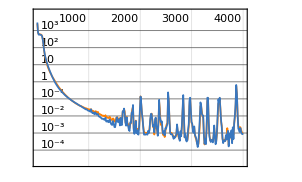
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:18s  examples/s:44348
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.83×10^-4
validation | ,,  loss:9.05×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-15,-33/2,-24,-49/2,-53/2,-29,-81/2,-83/2,-101/2,-59,-63,-147/2,-165/2,-173/2,-87,-88,-96,-100}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-14.9777,-16.5018,-24.0065,-24.5083,-26.4925,-29.,-40.5015,-41.5083,-50.4848,-58.9991,-62.9952,-73.4979,-82.4828,-86.4799,-86.9727,-87.9872,-96.0273,-99.8619}

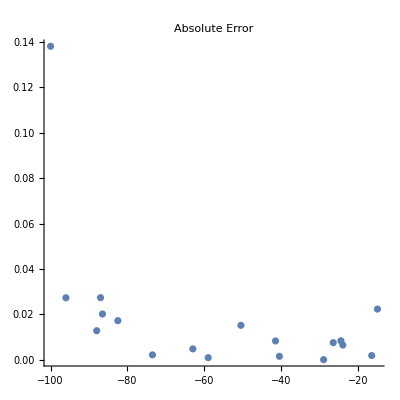

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

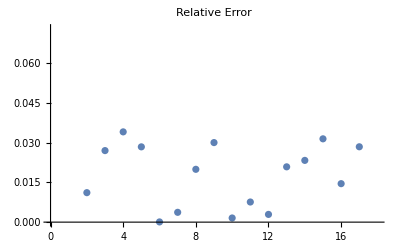

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0317603

## Comparing the real and imaginary parts of Kloosterman sums

```mathematica
minweight=-100;
coeffnum=30;
```

### Absolute values of part 1

```mathematica
cnc50w150abs1 = Table[If[Mod[w,12]==0,Table[ ψ1abs[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ1abs[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150abs1norm=Normalize/@cnc50w150abs1;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150abs1norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

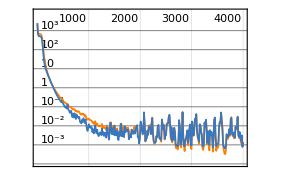
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:15s  examples/s:52883
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.18×10^-4
validation | ,,  loss:5.83×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-13,-14,-47/2,-24,-49/2,-41,-42,-44,-52,-63,-127/2,-129/2,-75,-159/2,-85,-177/2,-179/2,-195/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-12.9862,-13.9781,-23.553,-24.0385,-24.5241,-40.9001,-41.9487,-44.0116,-52.0027,-63.0056,-63.5005,-64.5098,-75.0047,-79.4928,-85.0017,-88.4656,-89.4739,-97.5091}

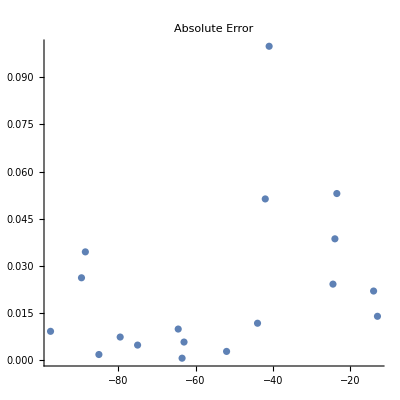

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

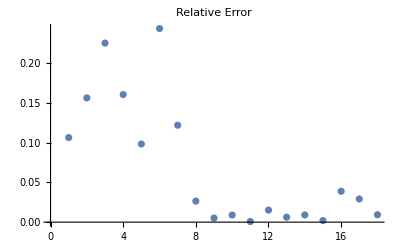

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0702341

### Real values of part 1

```mathematica
cnc50w150re1 = Table[If[Mod[w,12]==0,Table[ ψ1re[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ1re[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150re1norm=Normalize/@cnc50w150re1;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150re1norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

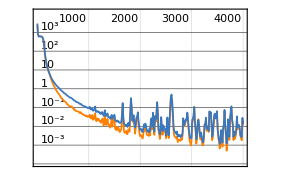
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:16s  examples/s:48043
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.8×10^-2
validation | ,,  loss:1.44×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-13,-27/2,-29/2,-43/2,-36,-45,-46,-113/2,-127/2,-64,-137/2,-75,-173/2,-93,-193/2,-97,-197/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-14.3518,-17.5069,-15.584,-14.4611,-21.5254,-35.994,-45.0078,-45.9739,-56.5226,-63.519,-63.9957,-68.5148,-75.0058,-86.4915,-93.0252,-96.5665,-97.029,-98.5011}

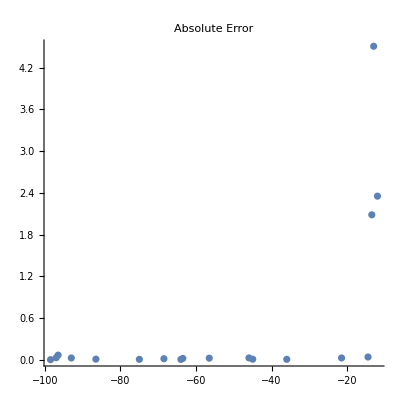

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

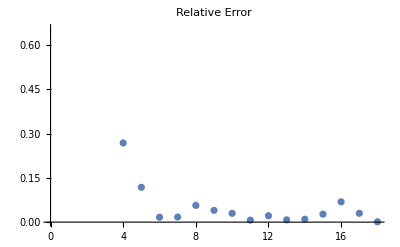

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

3.91242

### Absolute values of part 2

```mathematica
cnc50w150abs2 = Table[If[Mod[w,12]==0,Table[ ψ2abs[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ2abs[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150abs2norm=Normalize/@cnc50w150abs2;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150abs2norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

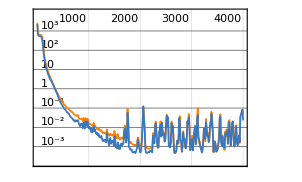
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:46741
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.81×10^-2
validation | ,,  loss:4.77×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-25/2,-13,-49/2,-25,-63/2,-35,-75/2,-87/2,-101/2,-103/2,-54,-72,-73,-153/2,-86,-185/2,-187/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-12.2684,-12.6735,-13.0893,-24.4973,-25.0022,-31.5062,-34.9512,-37.5227,-43.4946,-50.5049,-51.5018,-54.0035,-71.998,-72.9912,-76.5007,-85.9957,-92.4892,-93.4893}

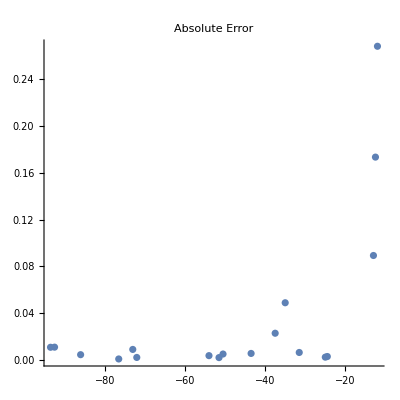

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

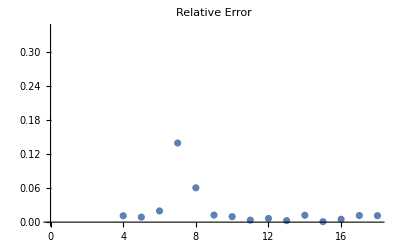

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.257055

### Real values of part 2

```mathematica
cnc50w150re2 = Table[If[Mod[w,12]==0,Table[ ψ2re[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ2re[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150re2norm=Normalize/@cnc50w150re2;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150re2norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

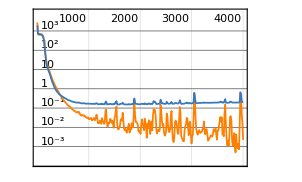
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:47423
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.93×10^-3
validation | ,,  loss:1.94×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-18,-45/2,-61/2,-65/2,-99/2,-101/2,-52,-53,-107/2,-123/2,-129/2,-133/2,-70,-75,-88,-91,-189/2,-197/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-17.9894,-22.5604,-30.5035,-32.4917,-49.4998,-50.4841,-51.9909,-52.999,-53.4809,-61.4894,-64.4768,-66.4838,-69.9518,-74.9958,-87.9364,-91.032,-94.4711,-98.2707}

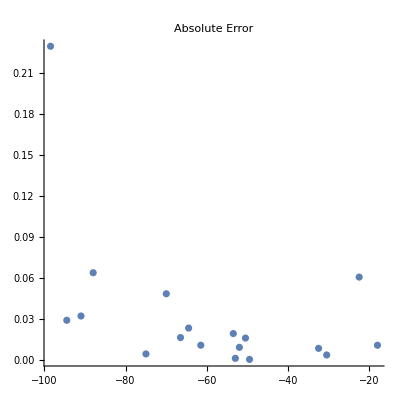

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

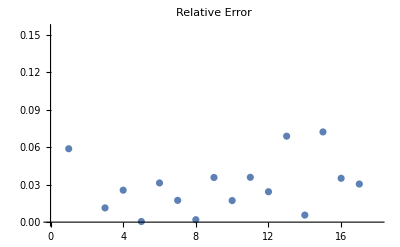

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0541437

## θ_1^m θ_2^n

0.351244 mean relative error for θ_1^m θ_2^n, with m,n∈[1,20] and q up to 𝒪(q^30) and 𝒪(u^50).

## Positive powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
prod1pos[t1_,m_, t2_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^m EllipticTheta[t2,u,q]^n,{q,0,nq}, {u,0,nu}];
If[(t1==1 || t1==2) && (t2==1 || t2==2), th2  = th1/q^(Mod[m+n,4]/4), th2  = th1 ];
cq = If[FreeQ[#,q]== False,  DeleteCases[CoefficientList[#, q],0],0 ] & /@ DeleteCases[CoefficientList[th2, u],0];
wt = Exponent[th1, u, List] + m/2 + n/2;
dt = Thread[cq -> wt];
If[(t1==1 || t1==2) && (t2==1 || t2==2), dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
t1t2m20n20q30u50mfpos1 = ParallelTable[prod1pos[1,m, 2, n,30,50], {m,20}, {n, 20}];
```

$Aborted

```mathematica
(*t1t2m20n20q30u50mfpos1 = ParallelTable[prod1pos[1,m, 2, n,30,50], {m,20}, {n, 20}];
DumpSave["t1t2m20n20q30u50mfpos1.mx", t1t2m20n20q30u50mfpos1];*)
(*t1t2m20n20q50u50mfpos1 = ParallelTable[prod1pos[1,m, 2, n,50,50], {m,20}, {n, 20}];
DumpSave["t1t2m20n20q50u50mfpos1.mx", t1t2m20n20q50u50mfpos1];*)
t1t2m20n20q70u100mfpos1 = ParallelTable[prod1pos[1,m, 2, n,70,100], {m,20}, {n, 20}];
DumpSave["t1t2m20n20q70u100mfpos1.mx", t1t2m20n20q70u100mfpos1];
```

```mathematica
<<t1t2m20n20q30u50mfpos1.mx
```

```mathematica
e1 = Flatten[t1t2m20n20q70u100mfpos1, 2];
```

```mathematica
fdata1 = e1;
```

```mathematica
Length /@ Keys[e1] // Union
```

{14,17,18,26,31,32,33,34,35}

```mathematica
nk1 = If[Length[#]>= 26, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
```

{26,31,32,33,34,35}

```mathematica
newkeys1 =nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

18193

{26}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
datasize = Length[data]
```

18193

```mathematica
trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]];
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
```

```mathematica
traindata=data[[trainpos]];
valdata=data[[valpos]];
testdata=data[[testpos]];
```

```mathematica
Length[traindata]
Length[valdata]
Length[testdata]
```

13644

2729

1820

```mathematica
enc=NetEncoder[{"Function",(Log[N[Abs[#]]]/.Indeterminate ->0 )& ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

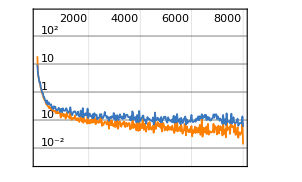
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:34min  examples/s:23910
data | ,,  training examples:6144  validation examples:1229  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.55×10^-2
validation | ,,  loss:5.57×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 11 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

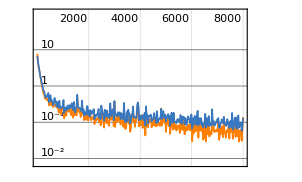
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:32min  examples/s:25568
data | ,,  training examples:6126  validation examples:1225  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.95×10^-2
validation | ,,  loss:5.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 21 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

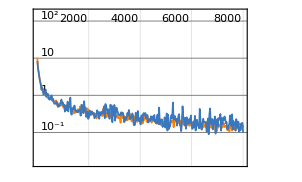
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1712000  rounds:8000  time:1.1h  examples/s:27933
data | ,,  training examples:13644  validation examples:2729  processed examples:109568000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.68×10^-2
validation | ,,  loss:5.92×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 31 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
testexact = testdata[[;;,2]];
```

```mathematica
testpred = tNet/@testdata[[;;,1]];
```

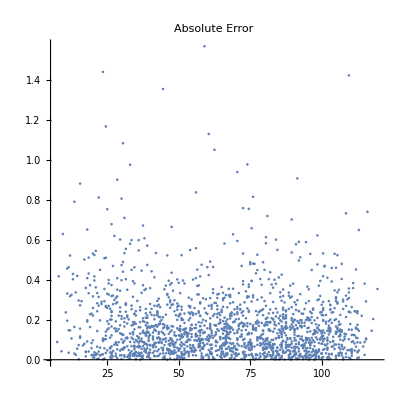

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

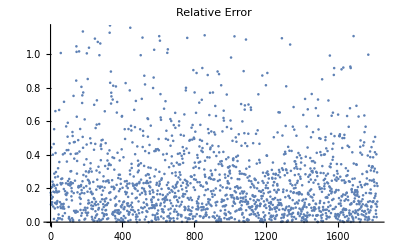

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.351244

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## θ_3^m θ_4^n

0.144678 mean relative error for θ_3^m θ_4^n, with m,n∈[1,20] and q up to 𝒪(q^30) and 𝒪(u^50).

## Positive powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
prod1pos[t1_,m_, t2_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^m EllipticTheta[t2,u,q]^n,{q,0,nq}, {u,0,nu}];
If[(t1==1 || t1==2) && (t2==1 || t2==2), th2  = th1/q^(Mod[m+n,4]/4), th2  = th1 ];
cq = If[FreeQ[#,q]== False,  DeleteCases[CoefficientList[#, q],0],0 ] & /@ DeleteCases[CoefficientList[th2, u],0];
wt = Exponent[th1, u, List] + m/2 + n/2;
dt = Thread[cq -> wt];
If[(t1==1 || t1==2) && (t2==1 || t2==2), dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
t3t4m20n20q30u50mfpos1 = ParallelTable[prod1pos[3,m, 4, n,30,50], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q30u50mfpos1.mx", t3t4m20n20q30u50mfpos1];
(*t3t4m20n20q50u50mfpos1 = ParallelTable[prod1pos[3,m, 4, n,50,50], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q50u50mfpos1.mx", t3t4m20n20q50u50mfpos1];*)
(*t3t4m20n20q70u100mfpos1 = ParallelTable[prod1pos[3,m, 4, n,70,100], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q70u100mfpos1.mx", t3t4m20n20q70u100mfpos1];*)
```

```mathematica
<<t1t2m20n20q30u50mfpos1.mx
```

```mathematica
e1 = Flatten[t3t4m20n20q30u50mfpos1, 2];
```

```mathematica
Length /@ Keys[e1] // Union
```

{8,15,22,23,26,29,30}

```mathematica
fdata1 = e1;
```

```mathematica
nk1 = If[Length[#]>= 22, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
```

{22,23,26,29,30}

```mathematica
newkeys1 =nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

9500

{22}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
datasize = Length[data]
```

9500

```mathematica
trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]];
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
```

```mathematica
traindata=data[[trainpos]];
valdata=data[[valpos]];
testdata=data[[testpos]];
```

```mathematica
Length[traindata]
Length[valdata]
Length[testdata]
```

7125

1425

950

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

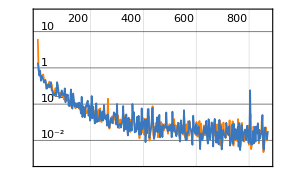
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:97664  rounds:872  time:6.0min  examples/s:17412
data | ,,  training examples:7125  validation examples:1425  processed examples:6250496  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.28×10^-2
validation | ,,  loss:1.55×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 22 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
testexact = testdata[[;;,2]];
```

```mathematica
testpred = tNet/@testdata[[;;,1]];
```

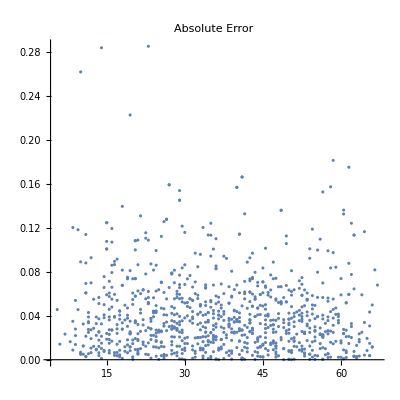

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

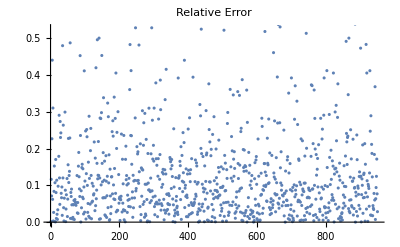

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.144678

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## θ_1^k θ_2^l θ_3^m θ_4^n

## Only Positive powers {k,l,m,n} > 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
allprod1pos[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = th1/q^((k+l)/4);
cq =DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt = Thread[cq -> wt];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]
]
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q70u80mfpos1, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,31,34,35,53,56,58,59,60,62,67,68,69,70}

minlen is a choice made to optimize data points and data quality.

```mathematica
minlen=60;
```

```mathematica
newkeystemp = If[Length[#]>= minlen, #, ##&[] ] & /@ Keys[rawdata];
Length /@  newkeystemp // Union
```

{60,62,67,68,69,70}

```mathematica
newkeys1 =newkeystemp[[All,;;minlen]];
newvalues1 = If[Length[Keys[#]]>= minlen, Values[#], ##&[] ] & /@ rawdata;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

19586

{60}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
datasize = Length[data]
```

{19586}

19586

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

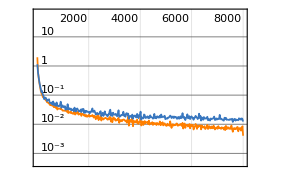
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1088000  rounds:8000  time:30min  examples/s:39097
data | ,,  training examples:8700  validation examples:1740  processed examples:69632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.14×10^-3
validation | ,,  loss:1.88×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

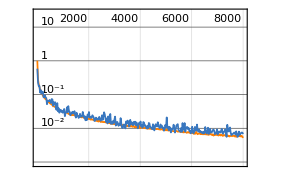
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1840000  rounds:8000  time:1.1h  examples/s:31091
data | ,,  training examples:14689  validation examples:2938  processed examples:117760000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.3×10^-3
validation | ,,  loss:8.9×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 60 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
testexact = testdata[[;;,2]];
```

```mathematica
testpred = tNet/@testdata[[;;,1]];
```

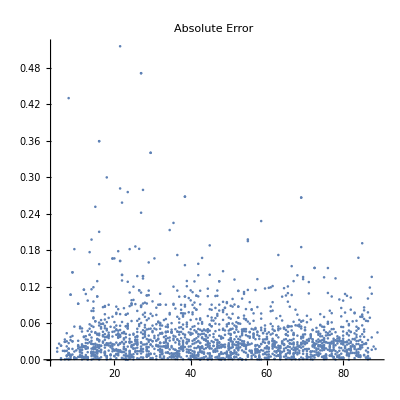

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

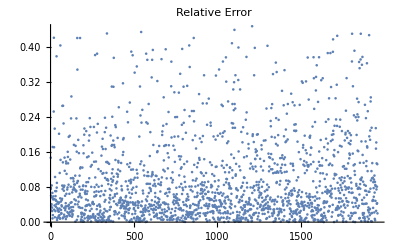

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.124924

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## Only Negative powers {k,l,m,n} < 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
tallk2l2m2n2q60u70mfneg1 = ParallelTable[allprod1neg[1, k, 2, l, 3,m, 4, n,60,70], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q60u70mfneg1.mx", tallk2l2m2n2q60u70mfneg1];
```

$Aborted

```mathematica
tallk2l2m2n2q20u30mfneg1 = ParallelTable[allprod1neg[1, k, 2, l, 3,m, 4, n,20,30], {k,-1,-3, -1},{l,-1,-3, -1}, {m,-1,-3, -1}, {n,-1,-3, -1}];
(*DumpSave["tallk2l2m2n2q20u30mfpos1.mx", tallk2l2m2n2q20u30mfpos1];*)
```

$Aborted

```mathematica
<<tallk5l5m5n5q70u80mfpos1.mx;
 <<t2n50q30u70mfpos1.mx;
```

```mathematica
rawdata = Flatten[tallk1l1m1n1q50u70mfneg1, 4];
```

```mathematica
e1[[;;2]]
```

{{-4,-16,-48,-112,-240,-480,-896,-1600,-2772,-4640,-7568,-12096,-18928,-29120,-44160,-65984,-97376,-142128,-205200,-293440,-415968,-584672,-815488,-1129344,-1553300,-2122848,-2884032,-3895808,-5234384,-6997440,-9308928,-12327168,-16252896,-21338944,-27904800,-36351792,-47181808,-61023136,-78658944,-101061760,-129439296,-165286464,-210447504,-267196864,-338331600,-427281856,-538251520,-676379904,-847935396,-1060556400}→3/2,{4/3,64/3,112,1216/3,1168,2944,20096/3,42496/3,28284,161408/3,295280/3,174336,899632/3,1509632/3,826496,3992576/3,6318176/3,3281472,5039440,22917376/3,11443232,50855552/3,74571904/3,36107264,155952500/3,74226304,105170112,443783168/3,619937936/3,286812928,395639552,542597120,740054176,3012219136/3,1355489440,1821201216,7307333296/3,9730731904/3,4301293952,17043340288/3,7474782912,9798524672,12799078096,49984149760/3,21617843760,83879000320/3,108153303808/3,46346571776,59411577036,75948616000}→7/2}

```mathematica
Length[rawdata]
Length /@ Keys[rawdata] // Union
```

823

{25,26,50,51}

```mathematica
newkeystemp = If[Length[#]>= 50, #, ##&[] ] & /@ Keys[rawdata];
Length /@  nk1 // Union
(*nk2 = If[Length[#]>= 26, #, ##&[] ] & /@ Keys[fdata2];
Length /@  nk2 // Union*)
```

{50,51}

```mathematica
minlen=Min[Length /@ newkeystemp];
```

```mathematica
newkeys =newkeystemp[[All,;;minlen]];
newvalues = If[Length[Keys[#]]>= minlen, Values[#], ##&[] ] & /@ rawdata;
```

```mathematica
Length[newkeys]
Length /@ newkeys // Union
Length[newkeys] == Length[newvalues]
```

572

{50}

True

```mathematica
data = Thread[newkeys->newvalues];
Dimensions[data]
datasize = Length[data]
```

{572}

572

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

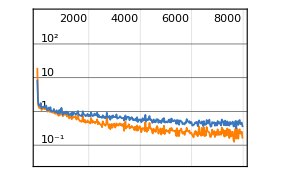
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:56000  rounds:8000  time:2.4min  examples/s:24720
data | ,,  training examples:402  validation examples:81  processed examples:3584000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.66×10^-1
validation | ,,  loss:2.46×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 25 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

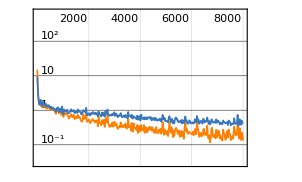
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:56000  rounds:8000  time:3.3min  examples/s:17998
data | ,,  training examples:402  validation examples:81  processed examples:3584000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.17×10^-1
validation | ,,  loss:2.15×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 25 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

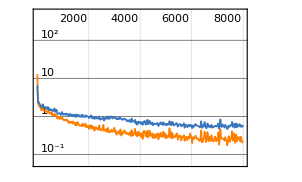
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:8000  time:3.8min  examples/s:22628
data | ,,  training examples:617  validation examples:123  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.56×10^-1
validation | ,,  loss:6.68×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, Method->{"ADAM","L2Regularization"->0.0001}, TargetDevice->"GPU"] (* 25 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

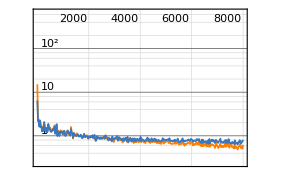
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:56000  rounds:8000  time:2.4min  examples/s:25194
data | ,,  training examples:429  validation examples:85  processed examples:3584000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.66×10^-1
validation | ,,  loss:8.48×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
testexact = testdata[[;;,2]];
```

```mathematica
testpred = tNet/@testdata[[;;,1]];
```

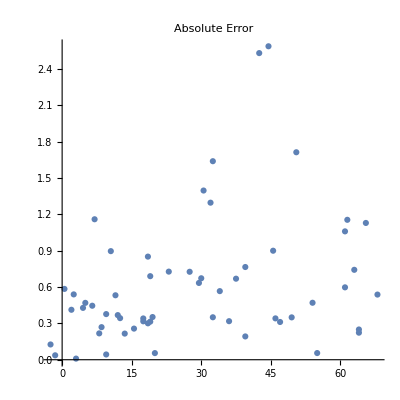

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

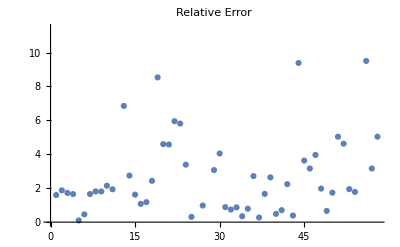

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

5.51576

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## k+l+m+n>0 (k,l,m,n need not be all > 0)

```mathematica
pwrs = klmn[5, 3]
```

{{3,4,-2,-3},{-4,4,4,-3},{-3,-1,2,4}}

```mathematica
(*p1 = allprodgen[40,50,pwrs[[;;3]]];*)
```

```mathematica
allprodgen[10,20, pwrs];
```

```mathematica
rawdata = rawData=Import["jacobi-klmn.txt",Path->NotebookDirectory[]];
```

```mathematica
textLines=StringSplit[rawData,"\n,"];
```

```mathematica
rawdata = p1
```

```mathematica
Values[rawdata];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{13,17,18,19,20,21,22}

```mathematica
newkeystemp = If[Length[#]>= 17, #, ##&[] ] & /@ Keys[rawdata];
Length /@  newkeystemp // Union
```

{17,18,19,20,21,22}

```mathematica
minlen=Min[Length /@ newkeystemp];
```

```mathematica
newkeys =newkeystemp[[All,;;minlen]];
newvalues = If[Length[Keys[#]]>= Min[Length /@ newkeystemp], Values[#], ##&[] ] & /@ rawdata;
```

```mathematica
Length[newkeys]
Length /@ newkeys// Union
Length[newkeys] == Length[newvalues]
```

6050

{17}

True

```mathematica
data = Thread[newkeys ->newvalues];
datasize = Length[data]
```

{6050}

6050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 17 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

## θ_1^k θ_2^l θ_3^m θ_4^n/Δ

## 2 η^3 = θ_2θ_3θ_4

## Setting k = 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
k1 = ParallelTable[allprod1pos[1, 0, 2, l, 3,m, 4, n,70,80], {l, 3},{m,3}, {n, 3}];
```

```mathematica
<<tallk5l5m5n5q70u80mfpos1.mx; <<t2n50q30u70mfpos1.mx;
```

```mathematica
e1 = Flatten[tallk0l5m5n5q70u80mfpos1, 4];
(*e2 = Flatten[t2n70q60u100mfpos1, 1];
e3 = Flatten[t3n70q60u100mfpos1, 1];
e4 = Flatten[t4n70q60u100mfpos1, 1];*)
```

```mathematica
e1[[;;2]]
```

{{-1,27,-125,343,-729,1331,-2197,3375}→7/2,{1/12,-209/4,-96,5429/12,96,768,-32935/12,864,-1920,-1056,30819/4,288,-2400,6720,4416,-346523/12,9504,-384,-5760,-7200,-5376,548701/12,12000,-20160,-3936,19872,30432,-9408,-471109/4,31008,3168,10272,-25728,1920,-36288}→11/2}

```mathematica
Length /@ Keys[e1] // Union
```

{8,14,26,31,34,35,36,48,52,53,59,60,61,62,69,70}

```mathematica
fdata1 = e1;
```

```mathematica
Values[fdata1];
```

```mathematica
Length /@ Keys[fdata1] // Union
```

{8,14,26,31,34,35,36,48,52,53,59,60,61,62,69,70}

```mathematica
nk1 = If[Length[#]>= 59, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
(*nk2 = If[Length[#]>= 26, #, ##&[] ] & /@ Keys[fdata2];
Length /@  nk2 // Union*)
```

{59,60,61,62,69,70}

```mathematica
newkeys1 =nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
(*newkeys2 =nk2[[All,;;Min[Length /@ nk2]]];
newvalues2 = If[Length[Keys[#]]>= 26, Values[#], ##&[] ] & /@ fdata2;*)
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

3988

{59}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
Dimensions[data]
datasize = Length[data]
```

{3988}

3988

```mathematica
Length @ Keys[data[[1]]]
data[[1]]
```

59

{1/12,-41/6,-209/4,441/2,-223/6,192,-2545/12,-8509/6,-96,-2665/6,23317/6,377/2,-30631/12,42431/6,2400,-49277/6,-12449,3648,-6417/2,576,14691/4,2999/3,62965/6,-2304,50499/2,41239/6,8832,-7047/2,-195623/6,-104475/2,-164507/12,40793,14496,-14400,-492091/6,-14208,255173/3,324863/6,-43505/2,724307/6,-21888,-4416,971399/12,-584357/6,10272,-231579/2,-125743/3,54144,-240007/6,100951/6,-19488,-605789/3,7200,-93504,13824,210905,335297/4,475533/2,1522205/6}→6

```mathematica
trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]];
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
```

```mathematica
traindata=data[[trainpos]];
valdata=data[[valpos]];
testdata=data[[testpos]];
```

```mathematica
Length[traindata]
Length[valdata]
Length[testdata]
```

2991

598

399

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

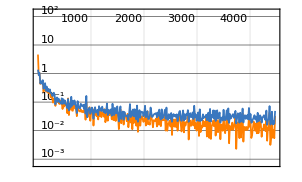
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:210251  rounds:4473  time:5.9min  examples/s:38282
data | ,,  training examples:2997  validation examples:599  processed examples:13456064  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.31×10^-1
validation | ,,  loss:1.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 48 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

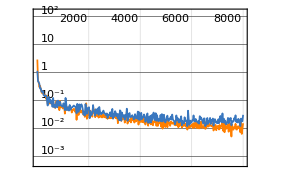
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:376000  rounds:8000  time:13min  examples/s:31393
data | ,,  training examples:2991  validation examples:598  processed examples:24064000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.26×10^-3
validation | ,,  loss:1.03×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 59 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
testexact = testdata[[;;,2]];
```

```mathematica
testpred = tNet/@testdata[[;;,1]];
```

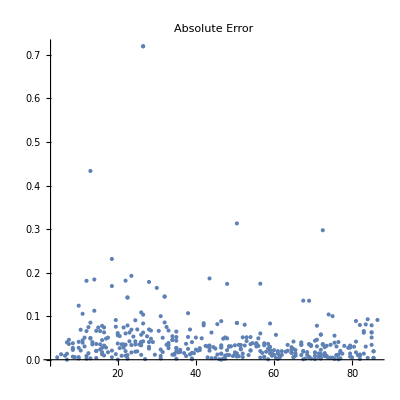

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

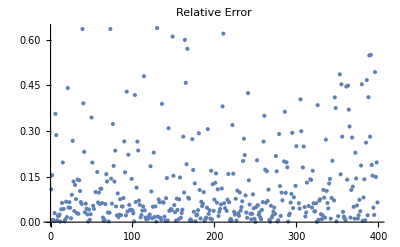

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.161518

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## u = 0

```mathematica
eta1pos[m_,  n_, nq_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[ EllipticTheta[2,0,q]^m EllipticTheta[3,0,q]^n EllipticTheta[4,0,q]^n,{q,0,nq}];
th2  = th1/q^(m/4);
cq = DeleteCases[CoefficientList[th2, q],0];
wt = m/2+2 n/2;
dt = cq -> wt;
Return[dt]]
```

```mathematica
th1  = Series[ EllipticTheta[2,0,q]^5 EllipticTheta[3,0,q]^5 EllipticTheta[4,0,q]^5,{q,0,10}]
```

32 q^(5/4)-480 q^(13/4)+2880 q^(21/4)-7840 q^(29/4)+3360 q^(37/4)+O[q]^(41/4)

```mathematica
eta1pos[5, 5, 10]
```

{{32,-480,2880,-7840,3360}→15/2}

```mathematica
etan500q200 = ParallelTable[eta1pos[n, n, 200],{n, 0, 500, 1/8}];
DumpSave["etan500q200.mx", etan500q200];
```

```mathematica
<<etan300q100.mx
```

```mathematica
etan100q50
```

```mathematica
e1 = Flatten[etan500q200, 3];
```

```mathematica
Values[fdata1];
```

```mathematica
Length /@ Keys[fdata1] // Union
```

{0,14,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
nk1 = If[Length[#]>= 70, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
```

{70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
newkeys1 =Simplify @ nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

2262

{70}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
Dimensions[data]
datasize = Length[data]
```

{2262}

2262

```mathematica
Length/@ Keys[data] // Union
```

{70}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 20000;
```

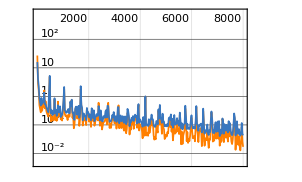
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.1min  examples/s:23336
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.09×10^-2
validation | ,,  loss:4.24×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 20 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

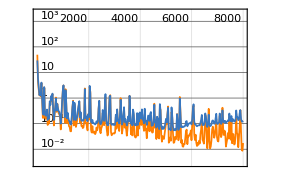
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:2.2min  examples/s:11670
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.49×10^-2
validation | ,,  loss:1.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 20 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

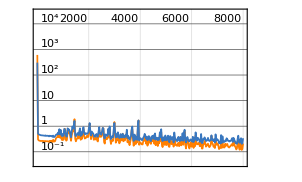
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.7min  examples/s:15094
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.79×10^-1
validation | ,,  loss:4.22×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

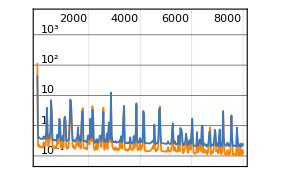
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.6min  examples/s:16311
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.11×10^-1
validation | ,,  loss:1.91×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

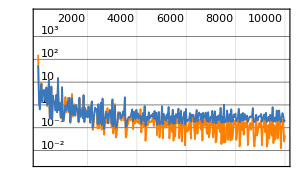
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.4min  examples/s:35160
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.7×10^-2
validation | ,,  loss:1.71×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

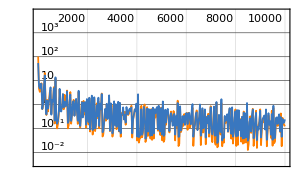
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:3.1min  examples/s:27529
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.71×10^-1
validation | ,,  loss:6.6×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

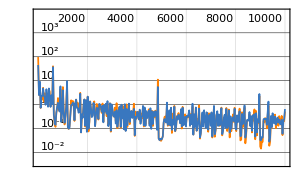
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.9min  examples/s:29141
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.96×10^-2
validation | ,,  loss:3.07×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

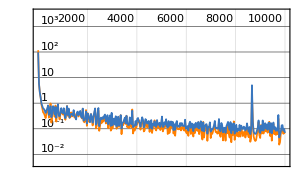
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.5min  examples/s:34530
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.18×10^-2
validation | ,,  loss:4.37×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU", LearningRate->0.0001] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

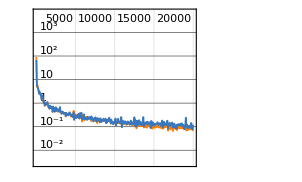
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:540000  rounds:20000  time:17min  examples/s:33878
data | ,,  training examples:1696  validation examples:339  processed examples:34560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.62×10^-2
validation | ,,  loss:5.35×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU", LearningRate->0.0001] (* etan500q200 70 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

## Individual θ_i without dividing by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

Generate data for all θ_i.

### θ_1

```mathematica
t1n30q30u60mfpos=ParallelTable[theta1[k,30,60],{k,30}];
(*DumpSave["t1n90q80u100mfpos1.mx", t1n90q80u100mfpos1];*)
```

```mathematica
rawdata=Flatten[t1n30q30u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{5,12,13,14,15}

```mathematica
minlen=12;
```

```mathematica
newkeystemp = If[Length[#]>= minlen, #, ##&[] ] & /@ Keys[rawdata];
Length /@  newkeystemp // Union
```

{12,13,14,15}

```mathematica
newkeys1 =newkeystemp[[All,;;minlen]];
newvalues1 = If[Length[Keys[#]]>= minlen, Values[#], ##&[] ] & /@ rawdata;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

660

{12}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
datasize = Length[data]
```

660

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

### θ_2

### θ_3

### θ_4

## Negative powers of θ_i

Generate data for all θ_i.

### θ_1

```mathematica
t1n30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
```

```mathematica
rawdata=Flatten[t1n30q30u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{5,12,13,14,15}

```mathematica
minlen=12;
```

```mathematica
datadefn[rawData_,minLen_]:=Module[{newkeysTemp,newKeys,newVals,data},
newkeysTemp = If[Length[#]>= minLen, #, ##&[] ] & /@ Keys[rawData];
newKeys =newkeysTemp[[All,;;minLen]];
newVals = If[Length[Keys[#]]>= minLen, Values[#], ##&[] ] & /@ rawData;
data = Thread[newKeys ->newVals];
Return[data]
]
```

```mathematica
data=datadefn[rawdata,minlen];
datasize= Length[data]
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc0=enc[data];
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc0, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

### θ_2

### θ_3

### θ_4

## Positive and negative powers together

Generate data for all θ_i.

### θ_1

```mathematica
krange=DeleteCases[Range[-70,70],0];
```

```mathematica
t1n70q50u100mfAll=ParallelTable[theta1[k,50,100],{k,krange}];
```

```mathematica
rawdata=Flatten[t1n70q50u100mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

```mathematica
minlen=
```

```mathematica
data=datadefn[rawdata,minlen]
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc0=enc[data];
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc0, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

### θ_2

### θ_3

### θ_4

## Individual θ_iwith division by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

Generate data for all θ_i.

### θ_1

```mathematica
t1n30q30u60mfpos=ParallelTable[theta1byΔ[k,30,60,3],{k,30}];
(*DumpSave["t1n90q80u100mfpos1.mx", t1n90q80u100mfpos1];*)
```

```mathematica
rawdata=Flatten[t1n30q30u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{5,12,13,14,15}

```mathematica
minlen=12;
```

```mathematica
newkeystemp = If[Length[#]>= minlen, #, ##&[] ] & /@ Keys[rawdata];
Length /@  newkeystemp // Union
```

{12,13,14,15}

```mathematica
newkeys1 =newkeystemp[[All,;;minlen]];
newvalues1 = If[Length[Keys[#]]>= minlen, Values[#], ##&[] ] & /@ rawdata;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

660

{12}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
datasize = Length[data]
```

660

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

### θ_2

### θ_3

### θ_4

## Negative powers of θ_i

Generate data for all θ_i.

### θ_1

```mathematica
t1n30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
```

```mathematica
rawdata=Flatten[t1n30q30u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{5,12,13,14,15}

```mathematica
minlen=12;
```

```mathematica
datadefn[rawData_,minLen_]:=Module[{newkeysTemp,newKeys,newVals,data},
newkeysTemp = If[Length[#]>= minLen, #, ##&[] ] & /@ Keys[rawData];
newKeys =newkeysTemp[[All,;;minLen]];
newVals = If[Length[Keys[#]]>= minLen, Values[#], ##&[] ] & /@ rawData;
data = Thread[newKeys ->newVals];
Return[data]
]
```

```mathematica
data=datadefn[rawdata,minlen];
datasize= Length[data]
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc0=enc[data];
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc0, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

### θ_2

### θ_3

### θ_4

## Positive and negative powers together

Generate data for all θ_i.

### θ_1

```mathematica
krange=DeleteCases[Range[-70,70],0];
```

```mathematica
t1n70q50u100mfAll=ParallelTable[theta1[k,50,100],{k,krange}];
```

```mathematica
rawdata=Flatten[t1n70q50u100mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

```mathematica
minlen=
```

```mathematica
data=datadefn[rawdata,minlen]
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc0=enc[data];
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc0, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc0, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

### θ_2

### θ_3

### θ_4